# The Wolfram data structure

# Murilo da Silva Baptista murilo.baptista@abdn.ac.uk

# Wolfram Data Framework (WDF)

Wolfram Data Framework (WDF): uses the Wolfram Language and the Wolfram Knowledgebase to provide a standardized representation of real-world constructs and data.

WDF finally makes it practical to put a wide range of types of data in truly computable form:

Dates, Quantities with Units, Time Series, Geo-positions, Graphics, Sounds, Images, Colours, Networks, Symbolic structures, Countries, Movies, Materials, Companies, Products, Species, Stars, Airlines, Words, Oceans, Schools, Albums, Polyhedra, Buildings, Asteroids, People, Foods…

# Work with All Kinds of Data

The Wolfram Data Framework (WDF) expresses everything the same way: tables and matrices, text, images, graphics, graphs and networks are all represented as symbols:

-Graphics-

[Brian WooBrian Wood Doing Data Science Better with Wolfram and the Multiparadigm Approach]

Import automatically detects the file type and structure of your data.

SemanticImport goes even further interpreting expressions in each field and displaying everything in an easy - to - view dataset. Import a file, automatically detecting and interpreting dates and cities:

```mathematica
sales=SemanticImport["ExampleData/RetailSales.tsv"]
```

## Wolfram Language Data Representation »paclet:guide/KnowledgeRepresentationAndAccess

Listpaclet:ref/List

Associationpaclet:ref/Association

Table :You can use Table to build up vectors,matrices,tensors,and other arrays. Table can do arbitrary iterating over list

Datasetpaclet:ref/Dataset a general hierarchical dataset containing nested lists and associations

EntityStorepaclet:ref/EntityStore — entity-based data/knowledgebase

Tabular : typically used for data where each column can be thought of as a variable and each row as a measurement . Typically, only a window of data is displayed .

# Lists

Lists are a basic way to collect things together in the Wolfram Language. {1,2,3} is a list of numbers. On their own, lists don’t do anything; they’re just a way to store things.

```mathematica
{1,2,3}//TableForm
```

1
2
3

```mathematica
{{1,2,3},{2,3}}//TableForm
```

1 | 2 | 3
2 | 3 |

But they are fundamental to understand the underlying structure of data. We will see several uses of Lists as we go

A tutorial to dealing with Lists can be seem in : Link

## A quick summary of positioning in lists/Matrices/Arrays

Let play around with indexes in a list of list (array or matrix).

```mathematica
matrix={{1,2,4},{4,6,19},{-1,-3,"Hello"}}
```

{{1,2,4},{4,6,19},{-1,-3,Hello}}

```mathematica
matrix//MatrixForm
```

(1 | 2 | 4
4 | 6 | 19
-1 | -3 | Hello)

```mathematica
matrix[[1;;2,1]]
```

{1,4}

```mathematica
Dimensions[matrix]
```

{3,3}

```mathematica
matrix1={{{1,2,4},{4,6,19},{-1,-3,"Hello"}},{{1+1,2+1,4+1},{4+1,6+1,19+1},{-1+1,-3+1,"Hello"+1}},{{1+2,2+2,4+2},{4+2,6+2,19+2},{-1+2,-3+2,"Hello"+2}}}
```

{{{1,2,4},{4,6,19},{-1,-3,Hello}},{{2,3,5},{5,7,20},{0,-2,1+Hello}},{{3,4,6},{6,8,21},{1,-1,2+Hello}}}

```mathematica
Dimensions[matrix1]
```

{3,3,3}

```mathematica
Dimensions[matrix1]
```

{3,3,3}

```mathematica
matrix1//
MatrixForm
```

((1
2
4) | (4
6
19) | (-1
-3
Hello)
(2
3
5) | (5
7
20) | (0
-2
1+Hello)
(3
4
6) | (6
8
21) | (1
-1
2+Hello))

```mathematica
matrix1[[3,2,2]]
```

8

```mathematica
matrix1[[1,3]]//MatrixForm
```

(-1
-3
Hello)

```mathematica
matrix1[[3,3,2]]
```

-1

Second Row

```mathematica
matrix1[[2]]
```

{{2,3,5},{5,7,20},{0,-2,1+Hello}}

```mathematica
matrix1[[2,3]]
```

{0,-2,1+Hello}

```mathematica
matrix1[[2,3,2]]
```

-2

```mathematica
matrix[[3,3]]
```

Hello

Flatten[] decreases the level of nested lists, basically transforming a row objects into column objects.

```mathematica
Flatten[matrix1]
```

{1,2,4,4,6,19,-1,-3,Hello,2,3,5,5,7,20,0,-2,1+Hello,3,4,6,6,8,21,1,-1,2+Hello}

```mathematica
matrix1//MatrixForm
```

((1
2
4) | (4
6
19) | (-1
-3
Hello)
(2
3
5) | (5
7
20) | (0
-2
1+Hello)
(3
4
6) | (6
8
21) | (1
-1
2+Hello))

Flatten up to level 1:

```mathematica
matrix1
```

{{{1,2,4},{4,6,19},{-1,-3,Hello}},{{2,3,5},{5,7,20},{0,-2,1+Hello}},{{3,4,6},{6,8,21},{1,-1,2+Hello}}}

```mathematica
Flatten[matrix1,1]//Dimensions
```

{9,3}

```mathematica
Flatten[matrix1,2]
```

{1,2,4,4,6,19,-1,-3,Hello,2,3,5,5,7,20,0,-2,1+Hello,3,4,6,6,8,21,1,-1,2+Hello}

```mathematica
Flatten[matrix1,2]//MatrixForm
```

(1
2
4
4
6
19
-1
-3
Hello
2
3
5
5
7
20
0
-2
1+Hello
3
4
6
6
8
21
1
-1
2+Hello)

```mathematica
matrix//MatrixForm
```

(1 | 2 | 4
4 | 6 | 19
-1 | -3 | Hello)

```mathematica
gg={{1,2},{2,3},{3,4}}//TableForm
```

1 | 2
2 | 3
3 | 4

```mathematica
Dimensions[gg]
```

{1}

```mathematica
gg[[1,2]]
```

2

```mathematica
gg={{1,2},{2,3},{3,4}}//Flatten//TableForm
```

1
2
2
3
3
4

```mathematica
gg[[1,2]]
```

2

```mathematica
Dimensions[gg]
```

{1}

```mathematica
matrix
```

{{1,2,4},{4,6,19},{-1,-3,Hello}}

```mathematica
matrix//MatrixForm
```

(1 | 2 | 4
4 | 6 | 19
-1 | -3 | Hello)

## Tables

-Graphics-

Table makes a list with a single element (a number, a function, a string...) repeated some specified number of times.

Tablepaclet:ref/Table[expr,n] → generates a list of n copies of expr.

a list with length 10 of only 5’s:

```mathematica
Table[5,10]
```

{5,5,5,5,5,5,5,5,5,5}

a list with length of list {i, 3} = {1, 2, 3}

```mathematica
Table[i, {i,3}]
```

{1,2,3}

```mathematica
Table[i^2, {i,3}]
```

{1,4,9}

a list of 10 “hellos”

```mathematica
Table["Hello", 10]
```

{Hello,Hello,Hello,Hello,Hello,Hello,Hello,Hello,Hello,Hello}

# Tables for higher - dimensional arrays, or lists of lists

You can use Table to build up vectors, matrices, tensors, and other arrays.

You can create a matrix 4 by 5:

```mathematica
Table[x,4,5]//MatrixForm
```

(x | x | x | x | x
x | x | x | x | x
x | x | x | x | x
x | x | x | x | x)

```mathematica
Table[1,4,5]//MatrixForm
```

(1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1)

You can create a 3 x 3 matrix with elements a[i,j]

```mathematica
Table[a[i,j],{i,3},{j,3}]
```

{{a[1,1],a[1,2],a[1,3]},{a[2,1],a[2,2],a[2,3]},{a[3,1],a[3,2],a[3,3]}}

```mathematica
MatrixForm[Table[a[i,j],{i,3},{j,3}]]
```

(a[1,1] | a[1,2] | a[1,3]
a[2,1] | a[2,2] | a[2,3]
a[3,1] | a[3,2] | a[3,3])

You can create a 5 x 3 matrix :

```mathematica
Grid[Table[a[i,j],{i,{2,3,5,7,11}},{j,{13,17,19}}]]
```

a[2,13] | a[2,17] | a[2,19]
a[3,13] | a[3,17] | a[3,19]
a[5,13] | a[5,17] | a[5,19]
a[7,13] | a[7,17] | a[7,19]
a[11,13] | a[11,17] | a[11,19]

Elements can also be an image:

```mathematica
a={-Graphics-}
```

{-Graphics-}

```mathematica
Table[a,3]
```

{{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
ff=Table[b[i,j],{i,{2,3,5,7,11}},{j,{13,17,19}}]
```

{{b[2,13],b[2,17],b[2,19]},{b[3,13],b[3,17],b[3,19]},{b[5,13],b[5,17],b[5,19]},{b[7,13],b[7,17],b[7,19]},{b[11,13],b[11,17],b[11,19]}}

```mathematica
TableForm[%]
```

b[2,13] | b[2,17] | b[2,19]
b[3,13] | b[3,17] | b[3,19]
b[5,13] | b[5,17] | b[5,19]
b[7,13] | b[7,17] | b[7,19]
b[11,13] | b[11,17] | b[11,19]

# Functions and indexes in Table

## Table takes an explicit form for functions:

```mathematica
Table[a[i,j],{i,3},{j,3}]
```

{{a[1,1],a[1,2],a[1,3]},{a[2,1],a[2,2],a[2,3]},{a[3,1],a[3,2],a[3,3]}}

or

```mathematica
Table[i+j,{i,3},{j,3}]
```

{{2,3,4},{3,4,5},{4,5,6}}

## Table can do arbitrary iterating over list :

```mathematica
Table[b[i,j],{i,{2,3,5,7,11}},{j,{13,17,19}}]//MatrixForm
```

(b[2,13] | b[2,17] | b[2,19]
b[3,13] | b[3,17] | b[3,19]
b[5,13] | b[5,17] | b[5,19]
b[7,13] | b[7,17] | b[7,19]
b[11,13] | b[11,17] | b[11,19])

# Associations

Keys and Values: Associations have keys and values.These data structures are used in other computer languages but known by different names :

Python and Julia call them dictionaries. Go and Scala call them maps. Perl and Ruby call them hashes.

Java calls it a HashMap.

Javascript calls it an object.

But they all work pretty similarly. Anyway, the keys of an Association are the things on the left hand side of the Rules. The key to understanding most Dataset operations is understanding Associations.

The Key-Value store of a NoSQL database is an association that has only 1 level associations.

Symbol | known as “vertical line”, or also as “the pipe”, “piping symbol”, “Sheffer stroke”, “vertical slash”, “think colon” or “divider line”.

An association in which key a is associated with value x, key b with value y, etc.:

```mathematica
<|a->x,b->y,c->z|>
```

<|a→x,b→y,c→z|>

# Querying Associations

Using our example before:

```mathematica
ee=<|a->x,b->y,c->z|>
```

<|0.84→x,b→y,c→z|>

Extract the value associated with key b:

```mathematica
ee[c]
```

z

Convert a list of rules to an association:

```mathematica
Head[{a->x,b->y,c->z}]
```

List

```mathematica
first=Association[{a->x,b->y,c->z}]
```

<|a→x,b→y,c→z|>

```mathematica
Head[first]
```

Association

```mathematica
Keys[first][[1]]
```

a

So, basically a "Key-Value store". Notice that if you add another list of associations, Wolfram shows Keys in the Columns:

Another Example :

```mathematica
assoc1=Association[{"class"->"1st","age"->29,"gender"->"female","survived"->True}]
```

<|class→1st,age→29,gender→female,survived→True|>

Keys are "transparent" for many operations:

A function applied to an association result in a new association with the Keys preserved but the values transformed

```mathematica
Map[f,<|a->4,b->2,c->1,d->5|>]
```

<|a→f[4],b→f[2],c→f[1],d→f[5]|>

Sort function  of an association produces an association and rank on the values of the association

```mathematica
Sort[<|a->4,b->"f",c->"a",d->5|>]
```

<|a→4,d→5,c→a,b→f|>

```mathematica
Sort[<|a->4,b->2,c->1,d->5|>]
```

<|c→1,b→2,a→4,d→5|>

Select function of an association creates another association with the Key -> values pairs selected according to the function applied to the values. 

Bellow: select what is inside the association if value of key-value is higher than 3:

```mathematica
Select[<|a->4,b->2,c->1,d->5|>,#>3&]
```

<|a→4,d→5|>

Total function produces a sum of all the values

```mathematica
Total[<|a->4,b->2,c->1,d->5|>]
```

12

Position gives keys that assumes a specific value as specified

```mathematica
Position[<|a->4,b->2,c->1,d->5|>,4]
```

{{Key[a]}}

```mathematica
Position[<|a->4,b->2,c->1,d->5|>,2]
```

{{Key[b]}}

```mathematica
Position[<|a->4,b->3,c->1,d->5|>,_Integer?PrimeQ]
```

{{Key[b]},{Key[d]}}

Append to an association:

```mathematica
Append[<|a->x,b->y,c->z|>,d->w]
```

<|a→x,b→y,c→z,d→w|>

Prepend to an association :

```mathematica
Prepend[<|a->x,b->y,c->z|>,d->w]
```

<|d→w,a→x,b→y,c→z|>

Keys extracts the list of keys:

```mathematica
Keys[<|a->x,b->y,c->z|>]
```

{a,b,c}

Associations can be modified by resetting values for an specific key:

```mathematica
assoc=<|a->x,b->y,c->z|>
```

<|a→x,b→y,c→z|>

```mathematica
assoc[b]=www
```

www

```mathematica
assoc
```

<|a→x,b→www,c→z|>

Delete entries from several associations, given a list of keys :

```mathematica
KeyDrop[{<|a -> 1, b -> 2|>, <|c -> 3, d -> 4|>}, {a, d}]
```

{<|b→2|>,<|{{2,4,5},{1},{3}}→3|>}

# More on Associations

## Associations

An association can be defined as follows.

```mathematica
person = <|"Name"->"Murilo","SSN"->"123-45-1234"|>
```

<|Name→Murilo,SSN→123-45-1234|>

You can access elements by position or Key.

By position you are treating the association as a list

```mathematica
person[[2]]
```

123-45-1234

```mathematica
person["SSN"]
```

123-45-1234

I you want to use by the Key them use only 1 Bracket [] to indicate that you are querying the association, treating it as a “function”.

```mathematica
person["Name"]
```

Murilo

This can be useful for keeping data on a collection of objects that are not uniform.

```mathematica
person["SSN"]
```

123-45-1234

```mathematica
student = <|"Name"->"Liu","SSN"->"987-65-4321","StudentID"->"12345678"|>;
```

```mathematica
student["StudentID"]
```

12345678

You can create arbitrary depth for associations by using associations as values of other associations (associations of associations!).

```mathematica
faculty=<|"Name"->"Smith","SSN"->"999-88-7777","HRInfo"-><|"Salary"->"12 Bars of Chocolate","Status"->"Faculty"|>|>;
```

Let us query the association :

```mathematica
faculty["HRInfo"]
```

<|Salary→12 Bars of Chocolate,Status→Faculty|>

```mathematica
faculty["HRInfo","Salary"]
```

12 Bars of Chocolate

```mathematica
faculty["HRInfo", "Status"]
```

Faculty

```mathematica
faculty//Dataset
```

just as a Key - Value NoSQL store ...

Let query as if it is list (or dataset, or matrix ...)

```mathematica
faculty[[3,2]]
```

Faculty

To get the Key from their value:

```mathematica
PositionIndex[faculty]["Smith"]
```

{Name}

```mathematica
FullForm[Position[faculty,"Smith"]]
```

List[List[Key["Name"]]]

```mathematica
FullForm[Position[faculty,"Smith"]]
```

List[List[Key["Name"]]]

#### Keys as strings or not? See Link

# Real World Data

Entity Types :  Wolfram Language entities represent physical entities as well as mathematical and other scientific concepts, and can be accessed via natural language input or programmatically retrieved and incorporated into complex computations.

```mathematica
Entity["Country","UnitedKingdom"]
```

United Kingdom

```mathematica
(ctrl=) specifies an entity using natural language:
Entity["Country","UnitedKingdom"]
```

```mathematica
Entity["Country", "UnitedKingdom"]
```

United Kingdom

Custom and dynamic entity types can also be introduced, from external entity stores, relational databases, etc.

The Wolfram Language provides access to curated, computable data about millions of entities across hundreds of entity types.

Entities have a type, a name, value, property, and belong to a class. All the entities of a certain type can belong to a class.

Refer to stackexchange for a nice discussion about the use of Entities!

#### Wolfram 14.1

=[UK] equivalent to ctrl= + UK

```mathematica
=[UK]
```

United Kingdom

## Difference between =, Ctrl = and =[ ]

= can only be entered at the beginning of a cell and then interprets the entire cell content as a free - form WolframAlpha query.

By contrast, CTRL = can be used to create an inline WolframAlpha interpretation cell that appears in the middle of an otherwise normal expression. For example, we can start by typing ImageDimensions[followed by CTRL +=] to create an inline cell.

=[query] interprets query using Wolfram|Alpha and computes the result, allowing for programmatic queries.

## Entities have a type and a name

Wolfram will try to identify the entity:

```mathematica
Entity["Country", "Brazil"]
```

Brazil

Above, "Brazil" is the name identifying an Entity and the type of the Entity is "Country"

You can do computation using the second option in the blue command box specifications. Later on...

Be careful, some entities have the same name (London city) in different countries, so

```mathematica
Entity["City",{"London","GreaterLondon","UnitedKingdom"}]
```

London

```mathematica
Entity["City",{"London","GreaterLondon","UnitedKingdom"}]
```

London

London

```mathematica
FullForm[%]
```

Entity["City",List["London","Ontario","Canada"]]

## Entities belong to a Class

Format : EntityClass["type", name] : represents a class of entities of the specified type identified by a name of the class.

Example: Represent all of the countries (“type”) in Europe (name of the class) :

```mathematica
EntityClass["Country","Europe"]
```

Europe

In the Entity type "Country", there are several countries (each being an Entity). They all belong to the class named Europe

Example: Ask for planets, and get the class of entities corresponding to planets in the solar system:

```mathematica
EntityClass["Planet",All]
```

```mathematica
EntityClass["Planet",All]//FullForm
```

```mathematica
EntityClass["Planet",All]
```

planets

Classes of entities are indicated by -Graphics-. 

The planets inside a class can be obtained by EntityList→ NEXT SLIDE

## There is a list of entities in a class

```mathematica
EntityList[EntityClass["Planet",All]]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

```mathematica
EntityClass["Exoplanet",All]
```

exoplanets

```mathematica
EntityList[%]//Shallow
```

{11 Comae Berenices b,11 Ursae Minoris b,14 Andromedae b,14 Herculis b,16 Cygni b,18 Delphini b,1RXS J160929.1-210524 b,24 Bootis b,24 Sextantis b,24 Sextantis c,«5204»}

## Entities have Properties (with values)

Format: EntityPropertypaclet:ref/EntityProperty[type,pname] 
represents a property identified by pname for use in EntityValuepaclet:ref/EntityValue.

Example: The property "cruise speed" of the entity type "Aircraft" :

```mathematica
EntityProperty["Aircraft","CruiseSpeed"]
```

cruise speed

Retrieve the cruise speed of the Boeing 737-700 :

```mathematica
Entity["Aircraft","Boeing737"]["CruiseSpeed"]
```

484.968 mi/h

```mathematica
Entity["Aircraft","Boeing737"][EntityProperty["Aircraft","CruiseSpeed"]]
```

484.968 mi/h

Or you could also have done (but see next slide) :

```mathematica
EntityValue[Entity["Aircraft","Boeing737"],EntityProperty["Aircraft","CruiseSpeed"]]
```

484.968 mi/h

Properties of an Entitypaclet:ref/Entity object can be obtained from Entitypaclet:ref/Entity[…]["property"]:

```mathematica
Entity["Country","Brazil"]["Population"]
```

216400000 people

```mathematica
Entity["Country","Brazil"][EntityProperty["Country","Pupils"]]
```

4.68156×10^7 people

All  the  properties  from  an  entity that has a “type”  can  be  obtained  using  EntityProperty["Entity
 type"]

```mathematica
EntityProperties[Entity["Country","Brazil"]];
```

```mathematica
EntityValue[Entity["Country","Brazil"],"Properties"];
```

## Entities have property values

Format: EntityValuepaclet:ref/EntityValue[entity,property]gives the value of the specified property for the given entity.

```mathematica
EntityValue[Entity["GeographicRegion","Europe"], "Population"]
```

745173774 people

```mathematica
EntityValue[Entity["Bridge","GoldenGateBridge::j6798"], "LongestSpan"]
```

4200. ft

## You can query about the entities in a class and their properties.

The bellow extracts the values for the entities inside the class "Planet", using the template EntityValue[class, property]. You will get the list of planets.

```mathematica
EntityValue["Planet","Entities"]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

You can also get the list of planets by Querying the class planets by :

```mathematica
EntityList[EntityClass["Planet",All]]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

You can extract all the "Properties" of all entities in the class "planet"

```mathematica
EntityValue["Planet","Properties"];
```

## Relevance of studying entity stores ?

Easy way to handle/pre-process/analyse data using the analytical/smart power of Mathematica

Suppose I want to treat data from child mortality in the world using United Nation data 
(Link). And in addition to the information provided by the UN dataset, I want to link it with other types of data or information, for example, I want to from the country name to get the nationality of a child from that country.

Notice file Imported has all types of mortality from all countries up to 2024.

```mathematica
countries=DeleteDuplicates[Import["/Users/murilo/Downloads/UNICEF-CME_DF_2021_WQ-1.0-download (2).csv",{"Data",2;;,2}]];
```

```mathematica
countries[[2]]
```

Angola

```mathematica
countryEntity = AssociationMap[Interpreter["Country"], countries];
```

```mathematica
countryEntity;
```

some problems could be manually resolved, for example:

```mathematica
countries = Replace[
countries,
{
"Bolivia (Plurinational State of)" -> "Bolivia",
"Micronesia (Federated States of)"-> "Micronesia"
},
{1}
];
```

Then, we can obtain nationality by

```mathematica
variable=Values[countryEntity];
```

```mathematica
variable[[1]]
```

Afghanistan

```mathematica
EntityValue[variable[[5]],"NationalityName"]
```

Andorran

```mathematica
Table[EntityValue[variable[[i]],"NationalityName"],{i,Length[variable]}]//Short
```

{Afghan,Angolan,Anguillan,Albanian,«227»,Yemeni,South African,Zambian,Zimbabwean}

We could then plot a Geo map indicating population, for the first 30 countries on the list.

```mathematica
variable[[1]]["Population"]
```

42200000 people

```mathematica
Table[variable[[i]]-> variable[[i]]["Population"],{i,30}];
```

```mathematica
GeoRegionValuePlot[Table[variable[[i]]-> variable[[i]]["Population"],{i,30}],GeoLabels->True]
```

-Graphics-

It is the format that data is imported to Mathematics from a relational dataset ! We will see that later.

Much information in the Wolfram language is stored using the Entity formalism.

# Mapping between the core relational and Entity framework [Wolfram Tutorial]

# Datasets

Datasetpaclet:ref/Dataset can represent not only full rectangular multidimensional arrays of data, but also arbitrary tree structures, corresponding to data with arbitrary hierarchical structure.

Depending on the data it contains, a Datasetpaclet:ref/Dataset object typically displays as a table or grid of elements.

Functions like Mappaclet:ref/Map, Selectpaclet:ref/Select, etc. (that we have seen to operate on lists) can also be applied directly to a Datasetpaclet:ref/Dataset by writing Mappaclet:ref/Map[f,dataset], Selectpaclet:ref/Select[dataset,crit], etc.

Subsets of the data in a Datasetpaclet:ref/Dataset object can be obtained by writing dataset[parts].

Datasetpaclet:ref/Dataset objects can also be queried using a specialized query syntax by writing dataset[query].

Take a look at the documentation about  Datasetpaclet:ref/Dataset

# A short introduction to Datasets

Create a Datasetpaclet:ref/Dataset object from tabular data:

## An example of a List of associations, a Table with named columns

```mathematica
dataset=Dataset[{
<|"a"->1,"b"->"x","c"->{1}|>,
<|"a"->2,"b"->"y","c"->{2,3}|>,
<|"a"->3,"b"->"z","c"->{3}|>,
<|"a"->4,"b"->"x","c"->{4,5}|>,
<|"a"->5,"b"->"y","c"->{5,6,7}|>,
<|"a"->6,"b"->"z","c"->{}|>}]
```

## Extracting from a Dataset

Let us extract the first 3 rows

```mathematica
dataset[1;;3]
```

Notice that there is not a double square Bracket "[[]]" as that would imply treating the Dataset as an “array”, but you can also use [[]].

Take the contents of a specific column :

```mathematica
dataset[All,"a"]
```

Take a subset of the rows and columns :

```mathematica
dataset[1;;4,{"a","b"}]
```

## Applying a function to a Dataset

Apply a function to the contents of a specific column :

```mathematica
dataset[Total,"a"]
```

21

Summing up data in columns "a" and "c":

```mathematica
dataset[All,{"a","c"}]
```

```mathematica
Map[Total,dataset[All,{"a","c"}]]
```

```mathematica
dataset[All,{"b","c"}]
```

```mathematica
dataset[StringJoin,"b"]
```

xyzxyz

Apply functions to each column independently:

```mathematica
dataset
```

we can define a function, and use to apply for the values of the keys:

```mathematica
f[x_]:=x^2;
```

```mathematica
f[4]
```

16

```mathematica
dataset[All,{"a"-> f,"b"->g,"c"->h}]
```

We could also use another format to define function, using format # &

```mathematica
ff=Sin[#]&;
```

```mathematica
dataset[All,{"a"->ff,"b"->g,"c"->h}]
```

Using the Map function :

In here, we first extract values from the Dataset object before calculating everything. But we can calculate things inside the argument of the Dataset object. Let us see how.

```mathematica
dataset[All,{"a","b"}]
```

```mathematica
Map[ff, dataset[All,{"a","b"}]]
```

This function can be any function, for example, a function to Select or to construct a Histogram

Selecting rows of key (column) "a" whose values are < 4 and “b” value is “x"

```mathematica
dataset[Select[#a<4&&#b=="x"&]]
```

We can only show a particular key - row (“c” in the example bellow), after selecting. Bellow will show column “c” if values in column “a” are smaller than 5.

```mathematica
dataset[Select[#a<5&],"c"]
```

Construct a Histogram of the keys "a"

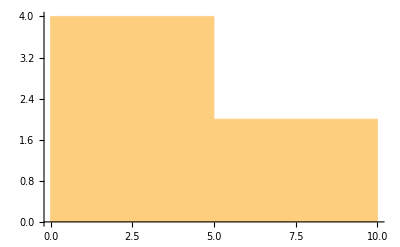

```mathematica
dataset[Histogram, "a"]
```

# Datasets as a List of Associations (a Table)

Load a dataset of passengers of the Titanic. You need to let Mathematica knows which type of data you want, bellow the type is “Dataset”, but it could be “Text”, “Texture”, “Sound”, “MachineLerning”, etc...

```mathematica
titanic=ExampleData[{"Dataset","Titanic"}]
```

```mathematica
Dimensions[titanic]
```

{1309,4}

```mathematica
Head[titanic]
```

Dataset

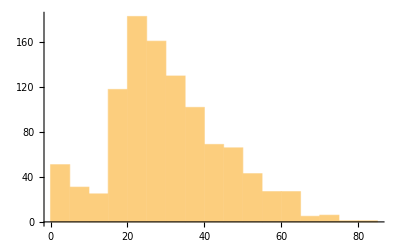

```mathematica
titanic[Histogram,"age"]
```

or for labels

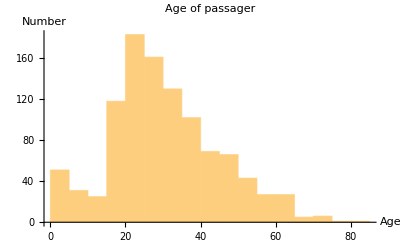

```mathematica
Histogram[titanic[All,"age"],PlotLabel->"Age of passager",AxesLabel->{"Age", "Number"}]
```

You can Groupby keys:

```mathematica
aa=titanic[GroupBy["class"]]
```

```mathematica
Dimensions[%]
```

{3}

```mathematica
aa[1][All,"age"];
```

# Datasets as an association of associations (indexed tables)

## a Table with named columns and named rows

```mathematica
planets=ExampleData[{"Dataset","Planets"}]
```

```mathematica
planets//Normal;
```

Earth has mass and radius (an association), and it has the Moon that has also mass and radius

```mathematica
planets["Mars","Moons"]
```

```mathematica
planets["Mars","Moons"]["Phobos"]
```

```mathematica
planets["Mars","Moons"]["Phobos"]["Radius"]
```

11.1 km

```mathematica
planets["Mars","Moons","Phobos","Radius"]
```

11.1 km

```mathematica
planets["Mars","Mass"]
```

6.41693×10^23 kg

```mathematica
planets//Normal
```

A Toy example to understand :

```mathematica
datasetNamedROWSCOLUMS=Dataset[{
<|"a"-><|"x"-> 1,"y"->-1|>,
"b"-><|"x"->10,"y"->{2,3}|>|>}]
```

Notice that now we have row but also column "keys"

Let us create a structure with a higher level

```mathematica
Dataset[{
<|"a"-><|"x"-> 1,"y"-><|z-> {2,5}|>|>,
"b"-><|"x"->10,"y"-><|z-> "Hello"|>|>|>}]
```

# Querying a Dataset

returning to our titanic Dataset

Shown in documentation several operators to function Query:

descending: Select, SortBy, KeySelect, DeleteMissing, Groupby...

A “descending” operator is applied to corresponding parts of the original dataset, before subsequent operators are applied at deeper levels.

ascending: Total, Min, Max, Mean, Histogram, Counts,...

An “ascending” operator is applied after all subsequent operators have been applied to deeper levels.

## Grouping by Gender:

```mathematica
titanic[GroupBy["sex"]]
```

```mathematica
titanicSex=Query[GroupBy["sex"]]@titanic
```

Or equivalently data input in Query as it were a function:

```mathematica
titanicSex=Query[GroupBy["sex"]][titanic];
```

Now I have a key for "male" and another for "female"

```mathematica
titanicSex["male"]
```

The same could have been done without Query:

```mathematica
titanic[GroupBy["sex"]]
```

## How many females and males were in the dataset?

```mathematica
titanic=ExampleData[{"Dataset","Titanic"}];
```

```mathematica
titanic[GroupBy["sex"],Length,#sex&]
```

## Grouping by Gender and calculating the average for the ages only:

Let us see how to query (obtain) the “age” row of the dataset:

```mathematica
Query[All,#age&][titanic];
```

We could have used also the information about the key/row name:

```mathematica
titanic[All,"age"];
```

```mathematica
Query[All,"age"][titanic];
```

The function bellow only Groups by sex and makes an average for all rows :

```mathematica
Query[GroupBy["sex"]][titanic];
```

```mathematica
Query[GroupBy[#sex&],Mean][titanic]
```

Notice that above, Mean counts missing as zeros, and division for total sum is made over the number of entries in the table (in this case passenger) - as Mathematica cannot “decide” which rows to use in the counting or not

Select only females :

```mathematica
Select[titanic,#sex=="female"&]
```

Now extract the ages

```mathematica
Select[titanic,#sex=="female"&][All,"age"]
```

```mathematica
Mean[Select[titanic,#sex=="female"&][[All,2]]]
```

1/466 (11134+78 Missing[])

```mathematica
11134/466//N
```

23.8927

To select only the key “age” and exclude missing in the average, do :

```mathematica
Query[GroupBy[#sex&],Mean,#age&][titanic]
```

Or, do it directly but DeleteMissing to take Mean:

Select all the ages for females

```mathematica
Query[GroupBy[#sex&]][titanic]
```

```mathematica
Query[GroupBy[#sex&]][titanic]["female"][All,"age"];
```

```mathematica
Mean[DeleteMissing[Query[GroupBy[#sex&]][titanic]["female"][All,"age"]]]//N
```

28.6959

```mathematica
11134/(466-78)//N
```

28.6959

## Grouping by gender and calculating the average age of the people that survived or not

bellow are the people that survived. Notice that True and False are boolean variables

Another way to select would be to use Select function (without a Query Function)

```mathematica
Select[titanic,#survived ==TrueQ[True]&& #sex=="female"&];
```

or :

```mathematica
Select[titanic,#survived ==True&& #sex=="female"&]
```

```mathematica
Query[Select[#survived==TrueQ[True]&]] @ titanic
```

bellow the female that survived

```mathematica
femalesurvive=Query[Select[#survived==TrueQ[True]&& #sex=="female"&]] @ titanic
```

Some ages do not exist. So, we can exclude them to calculate, for example doing:

```mathematica
femalesurvive[[All,"age"]];
```

```mathematica
DeleteMissing[femalesurvive[[All,"age"]]]//Mean
```

2177/73

```mathematica
N[%]
```

29.8219

If not have used DeleteMissing:

```mathematica
femalesurvive[[All,"age"]]//Mean
```

1/339 (8708+47 Missing[])

# Datasets and Associations

## Watch the You Tube videos by Andreas Lauschke :

Part 1

Part 2

Part 3

# Dataset versus Entity Store

As rule of thumb:

Datasets -> Tabular data, e.g. data that comes in an Excel Sheet, allowing a nested list of lists of the same data and hierarchical (list of list of different data types)

EntityStores -> Relational  data, such as data from an SQL database

However, for more complex data that involve different validations over time coming from different publications, one might consider to use a hybrid databases, see discussion by Stephan Schiffels.

## Tabular, NOTICE that it is an EXPERIMENTAL function

Tabular provides a very streamlined and efficient way to handle tables (structured) of data laid out in rows and columns. Can handle gigabytes of data both in core and out of core.

typically used for data where each column can be thought of as a variable and each row as a measurement.

```mathematica
Clear["data"]
```

```mathematica
data=Tabular[{{1,2,-1},{3,4,0.3}},{"a","b","c"}]
```

Extracting works similar to Dataset

```mathematica
data[All,{"a","b"}]
```

Select as well

```mathematica
Select[data,#a>=2&]
```

From Dataset to Tabular, and doing similar calculations as before.

```mathematica
titanic;
```

```mathematica
titanicTab=Tabular[titanic]
```

Mean already take into consideration Missing data

```mathematica
Select[titanicTab,#survived ==True&& #sex=="female"&][All,"age"]//Normal
```

{29,63,53,18,24,26,50,32,47,42,29,19,35,30,58,45,22,44,59,60,41,53,58,14,36,Missing[],76,47,33,36,30,Missing[],26,22,39,64,55,36,64,38,33,27,17,54,27,48,48,23,38,54,Missing[],Missing[],24,28,23,60,30,Missing[],22,48,35,35,22,45,Missing[],19,58,45,25,49,35,24,52,16,44,51,35,35,38,Missing[],45,39,49,30,55,16,51,21,58,15,16,18,24,Missing[],33,37,31,23,19,39,22,22,17,30,56,43,33,33,54,18,21,48,24,35,30,40,39,18,23,40,Missing[],43,52,62,48,18,39,Missing[],39,Missing[],35,60,55,31,45,50,21,31,36,28,36,36,19,4,12,36,19,24,15,40,20,36,42,22,35,25,45,28,8,31,22,48,28,24,18,34,34,27,30,29,34,24,6,7,45,24,24,48,55,20,54,29,17,24,23,24,Missing[],45,1,3,22,17,Missing[],34,42,24,13,41,14,29,50,21,19,32,2,8,33,30,28,24,50,21,25,18,20,30,30,40,50,28,27,31,31,12,40,33,29,4,29,1,5,33,26,35,16,18,18,19,17,5,38,45,13,33,1,1,5,24,18,22,16,22,36,17,30,Missing[],36,1,33,19,30,23,22,5,16,Missing[],31,24,45,Missing[],26,22,2,22,27,Missing[],Missing[],1,27,4,Missing[],Missing[],4,26,22,23,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],15,Missing[],27,Missing[],Missing[],Missing[],Missing[],24,Missing[],Missing[],Missing[],15,1,19,14,18,26,22,Missing[],Missing[],Missing[],22,Missing[],31,Missing[],Missing[],Missing[],Missing[],21,1,24,4,Missing[],18,Missing[],23,16,Missing[],9,29,18,63,38,47,15}

```mathematica
Select[titanicTab,#survived ==True&& #sex=="female"&][All,"age"]//Mean
```

29.8219